函数 f(Z)=1/Z

```mathematica
ComplexExpand[1/(X+I Y)]
```

X/(X^2+Y^2)-(ⅈ Y)/(X^2+Y^2)

避开原点

函数 f(Z)=1/(2 Z^2)

```mathematica
ComplexExpand[1/(2(X+I Y)^2)]
```

X^2/(2 (X^2+Y^2)^2)-(ⅈ X Y)/((X^2+Y^2)^2)-Y^2/(2 (X^2+Y^2)^2)

避开原点

函数 f(Z)=√2 √Z

```mathematica
ComplexExpand[√2 √(X+I Y)]
```

√2 (X^2+Y^2)^(1/4) Cos[1/2 Arg[X+ⅈ Y]]+ⅈ √2 (X^2+Y^2)^(1/4) Sin[1/2 Arg[X+ⅈ Y]]

```mathematica
Plot3D[{Arg[X+ⅈ Y],ArcTan[Y/X]},{X,0,1},{Y,0,1}]
```

-Graphics3D-

```mathematica
√2 (X^2+Y^2)^(1/4) Cos[1/2 ArcTan[Y/X]]+ⅈ √2 (X^2+Y^2)^(1/4) Sin[1/2 ArcTan[Y/X]]
```

避开原点

```mathematica
Plot3D[{Arg[X+ⅈ Y]},{X,-1,1},{Y,-1,1},PlotStyle-> Blue];
ContourPlot3D[x^2+y^2==1,{x,-2,2},{y,-2,2},{z,-Pi,Pi}];
Show[%%,%]
```

-Graphics3D-

函数 f(Z)=√2/√Z

```mathematica
ComplexExpand[√2/√(X+I Y)]
```

(√2 Cos[1/2 Arg[X+ⅈ Y]])/((X^2+Y^2)^(1/4))-(ⅈ √2 Sin[1/2 Arg[X+ⅈ Y]])/((X^2+Y^2)^(1/4))

```mathematica
(√2 Cos[1/2 ArcTan[Y/X]])/((X^2+Y^2)^(1/4))-(ⅈ √2 Sin[1/2 ArcTan[Y/X]])/((X^2+Y^2)^(1/4))
```

避开原点

函数 f(Z)=Sin[Z]

```mathematica
ComplexExpand[Sin[(X+I Y)]]
```

Cosh[Y] Sin[X]+ⅈ Cos[X] Sinh[Y]

函数 f(Z)=Cos[Z]

```mathematica
ComplexExpand[Cos[(X+I Y)]]
```

Cos[X] Cosh[Y]-ⅈ Sin[X] Sinh[Y]

参数方程

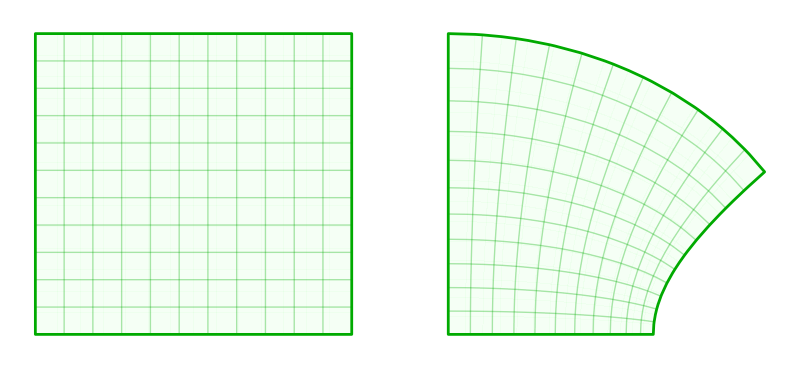

```mathematica
{fig1,fig2}=With[{z=x+I*y},ParametricPlot[ReIm[#],{x,0,1},{y,0,1},Mesh->10,PlotStyle->LightGreen,MeshStyle->Directive[Thick,Darker[Green]],BoundaryStyle->Directive[Thickness[.005],Darker[Green]],Frame->False,Axes->False]]&/@{z,Sin[z]};
GraphicsRow[{fig1,fig2}]
```

```mathematica
x=1/3 Cosh[(3 π Y)/5] Sin[(3 π X)/5];
y=1/3 Cos[(3 π X)/5] Sinh[(3 π Y)/5];
```

```mathematica
ParametricPlot[{x,y}, {X,0,1},{Y,0,1},PlotRange->All,PlotStyle->Blue];
ParametricPlot[{X,Y}, {X,0,1},{Y,0,1},PlotRange->All,PlotStyle->Gray];
RefCur=Show[%%,%];
```

```mathematica
Manipulate[Show[RefCur,ListPlot[Evaluate[{{x,y},{X,Y}}/.{X-> a,Y-> b}],PlotStyle->PointSize[Large]]],{a,0,1},{b,0,1}]
```

变形梯度张量

```mathematica
F={{D[x,X],D[x,Y]},{D[y,X],D[y,Y]}}
```

{{Cos[X] Cosh[Y],Sin[X] Sinh[Y]},{-Sin[X] Sinh[Y],Cos[X] Cosh[Y]}}

利用F = AG 求A

```mathematica
G={{√(D[x,X]^2+D[y,X]^2),0},{0,√(D[x,X]^2+D[y,X]^2)}};
Simplify[G,0<X<1&&0<Y<1]
```

{{(√(Cos[2 X]+Cosh[2 Y]))/(√2),0},{0,(√(Cos[2 X]+Cosh[2 Y]))/(√2)}}

```mathematica
A=F.Inverse[G]//Simplify
```

{{(√2 Cos[X] Cosh[Y])/(√(Cos[2 X]+Cosh[2 Y])),(√2 Sin[X] Sinh[Y])/(√(Cos[2 X]+Cosh[2 Y]))},{-(√2 Sin[X] Sinh[Y])/(√(Cos[2 X]+Cosh[2 Y])),(√2 Cos[X] Cosh[Y])/(√(Cos[2 X]+Cosh[2 Y]))}}

可见这个A就是一个旋转张量

```mathematica
A.Transpose[A]//Simplify
```

{{1,0},{0,1}}